```mathematica
ClearAll["Global`*"]

(* Lithium Niobate properties *)
nNotTensorLN = {{no,0,0},{0,no,0},{0,0,ne}};
kNotTensorLN = {{ko,0,0},{0,ko,0},{0,0,ke}};
ϵrTensorLN=(nNotTensorLN+ⅈ*kNotTensorLN)^2;
βTensorLN=Inverse[ϵrTensorLN];

CVoigtLN={{c11,c12,c13,c14,0,0},{c12,c11,c13,-c14,0,0},{c13,c13,c33,0,0,0},{c14,-c14,0,c44,0,0},{0,0,0,0,c44,c14},{0,0,0,0,c14,(c11-c12)/2}};
CVoigtLNvalues={c11-> 198.83*10^9,c12-> 54.64*10^9,c13-> 68.23*10^9,c14-> 7.83*10^9,c33-> 235.71*10^9,c44-> 59.86*10^9};

PVoigtLN={{p11,p12,p13,p14,0,0},{p12,p11,p13,-p14,0,0},{p31,p31,p33,0,0,0},{p41,-p41,0,p44,0,0},{0,0,0,0,p44,p41},{0,0,0,0,p14,(p11-p12)/2}};
PVoigtLNvalues={p11-> -0.026, p12-> 0.088, p13-> 0.134, p14-> -0.083, p31-> 0.177,p33-> 0.07,p41-> -0.151, p44-> 0.145};

dVoigtLN={{0,0,0,0,d31,-d22},{-d22,d22,0,d31,0,0},{d31,d31,d33,0,0,0}};
dVoigtLNvalues = {d31-> -4.3*10^-12,d33->-27*10^-12,d22->2.1*10^-12} ;

rVoigtLN={{0,-r22,r13},{0,r22,r13},{0,0,r33},{0,r42,0},{r42,0,0},{-r22,0,0}};
rVoigtLNvalues = {r13->9.6*10^-12,r22-> 6.8*10^-12,r33->30.9*10^-12,r42->32.6*10^-12} ;

eVoigtLN={{0,0,0,0,e15,-e22},{-e22,e22,0,e15,0,0},{e31,e31,e33,0,0,0}};
eVoigtLNvalues = {e15->3.65,e31-> 0.31,e33->1.72,e22->2.39} ;
(*--------------------*)

(* Visualization/Plotting - The units in the 'values' vectors are in S.I. *)
ϵrTensorLN//MatrixForm
βTensorLN//MatrixForm
{CVoigtLN//MatrixForm,CVoigtLN/.CVoigtLNvalues//N//MatrixForm}
{PVoigtLN//MatrixForm, PVoigtLN/.PVoigtLNvalues//N//MatrixForm}
{dVoigtLN//MatrixForm, dVoigtLN/.dVoigtLNvalues//N//MatrixForm}
{rVoigtLN//MatrixForm, rVoigtLN/.rVoigtLNvalues//N//MatrixForm}
{eVoigtLN//MatrixForm, eVoigtLN/.eVoigtLNvalues//N//MatrixForm}
(*--------------------*)
```

((ⅈ ko+no)^2 | 0 | 0
0 | (ⅈ ko+no)^2 | 0
0 | 0 | (ⅈ ke+ne)^2)

(1/(ⅈ ko+no)^2 | 0 | 0
0 | 1/(ⅈ ko+no)^2 | 0
0 | 0 | 1/(ⅈ ke+ne)^2)

{(c11 | c12 | c13 | c14 | 0 | 0
c12 | c11 | c13 | -c14 | 0 | 0
c13 | c13 | c33 | 0 | 0 | 0
c14 | -c14 | 0 | c44 | 0 | 0
0 | 0 | 0 | 0 | c44 | c14
0 | 0 | 0 | 0 | c14 | (c11-c12)/2),(1.9883×10^11 | 5.464×10^10 | 6.823×10^10 | 7.83×10^9 | 0. | 0.
5.464×10^10 | 1.9883×10^11 | 6.823×10^10 | -7.83×10^9 | 0. | 0.
6.823×10^10 | 6.823×10^10 | 2.3571×10^11 | 0. | 0. | 0.
7.83×10^9 | -7.83×10^9 | 0. | 5.986×10^10 | 0. | 0.
0. | 0. | 0. | 0. | 5.986×10^10 | 7.83×10^9
0. | 0. | 0. | 0. | 7.83×10^9 | 7.2095×10^10)}

{(p11 | p12 | p13 | p14 | 0 | 0
p12 | p11 | p13 | -p14 | 0 | 0
p31 | p31 | p33 | 0 | 0 | 0
p41 | -p41 | 0 | p44 | 0 | 0
0 | 0 | 0 | 0 | p44 | p41
0 | 0 | 0 | 0 | p14 | (p11-p12)/2),(-0.026 | 0.088 | 0.134 | -0.083 | 0. | 0.
0.088 | -0.026 | 0.134 | 0.083 | 0. | 0.
0.177 | 0.177 | 0.07 | 0. | 0. | 0.
-0.151 | 0.151 | 0. | 0.145 | 0. | 0.
0. | 0. | 0. | 0. | 0.145 | -0.151
0. | 0. | 0. | 0. | -0.083 | -0.057)}

{(0 | 0 | 0 | 0 | d31 | -d22
-d22 | d22 | 0 | d31 | 0 | 0
d31 | d31 | d33 | 0 | 0 | 0),(0. | 0. | 0. | 0. | -4.3×10^-12 | -2.1×10^-12
-2.1×10^-12 | 2.1×10^-12 | 0. | -4.3×10^-12 | 0. | 0.
-4.3×10^-12 | -4.3×10^-12 | -2.7×10^-11 | 0. | 0. | 0.)}

{(0 | -r22 | r13
0 | r22 | r13
0 | 0 | r33
0 | r42 | 0
r42 | 0 | 0
-r22 | 0 | 0),(0. | -6.8×10^-12 | 9.6×10^-12
0. | 6.8×10^-12 | 9.6×10^-12
0. | 0. | 3.09×10^-11
0. | 3.26×10^-11 | 0.
3.26×10^-11 | 0. | 0.
-6.8×10^-12 | 0. | 0.)}

{(0 | 0 | 0 | 0 | e15 | -e22
-e22 | e22 | 0 | e15 | 0 | 0
e31 | e31 | e33 | 0 | 0 | 0),(0. | 0. | 0. | 0. | 3.65 | -2.39
-2.39 | 2.39 | 0. | 3.65 | 0. | 0.
0.31 | 0.31 | 1.72 | 0. | 0. | 0.)}

```mathematica
VoigtFunc[i_,j_]:=If[i==1&&j==1,1,
If[i==2&&j==2,2,
If[i==3&&j==3,3,
If[i==2&&j==3,4,
If[i==3&&j==2,4,
If[i==1&&j==3,5,
If[i==3&&j==1,5,
If[i==1&&j==2,6,
If[i==2&&j==1,6,7]]]]]]]]];

InvVoigtFunc[ij_]:=If[ij==1,{1,1},
If[ij==2,{2,2},
If[ij==3,{3,3},
If[ij==4,{2,3},
If[ij==5,{1,3},
If[ij==6,{1,2},{4,4}]]]]]];

a=RotationMatrix[θy,{0,1,0}].RotationMatrix[θx,{1,0,0}].RotationMatrix[θz,{0,0,1}]//Simplify;
```

```mathematica
ϵrTensorLNRot=a.ϵrTensorLN.Transpose[a];
βTensorLNRot=a.βTensorLN.Transpose[a];

CTensorLNRot[i_,j_,k_,l_]:=Sum[Sum[Sum[Sum[a[[i,α]]*a[[j,β]]*a[[k,γ]]*a[[l,δ]]*CVoigtLN[[VoigtFunc[α,β],VoigtFunc[γ,δ]]],{α,1,3,1}],{β,1,3,1}],{γ,1,3,1}],{δ,1,3,1}];
PTensorLNRot[i_,j_,k_,l_]:=Sum[Sum[Sum[Sum[a[[i,α]]*a[[j,β]]*a[[k,γ]]*a[[l,δ]]*PVoigtLN[[VoigtFunc[α,β],VoigtFunc[γ,δ]]],{α,1,3,1}],{β,1,3,1}],{γ,1,3,1}],{δ,1,3,1}];

dTensorLNRot[i_,j_,k_]:=Sum[Sum[Sum[a[[i,α]]*a[[j,β]]*a[[k,γ]]*dVoigtLN[[α,VoigtFunc[β,γ]]],{α,1,3,1}],{β,1,3,1}],{γ,1,3,1}];

rTensorLNRot[i_,j_,k_]:=Sum[Sum[Sum[a[[i,α]]*a[[j,β]]*a[[k,γ]]*rVoigtLN[[VoigtFunc[α,β],γ]],{α,1,3,1}],{β,1,3,1}],{γ,1,3,1}];

eTensorLNRot[i_,j_,k_]:=Sum[Sum[Sum[a[[i,α]]*a[[j,β]]*a[[k,γ]]*eVoigtLN[[α,VoigtFunc[β,γ]]],{α,1,3,1}],{β,1,3,1}],{γ,1,3,1}];
```

```mathematica
(* this is the part that we translate the syntax of Mathematica to the COMSOL syntax *)

ToComsolRule = {"**"-> "^","θz"-> "Rz_LN","θy"-> "Ry_LN","θx"-> "Rx_LN","Cos"-> "cos","Sin"-> "sin","COS"-> "cos","SIN"-> "sin","no"->"no_ext(lambda0)","ne"->"ne_ext(lambda0)","ko"->"ko_ext(lambda0)","ke"->"ke_ext(lambda0)","n"->"n_ext(lambda0)","k"->"k_ext(lambda0)"};
```

```mathematica
(* This export the relative permittivity ϵr as epsrij.csv, for each pair (i,j) *)
Do[Export["epsr"<>ToString[i]<>ToString[j]<>"_LN.csv",StringReplace[ToString[FortranForm[Simplify[ϵrTensorLNRot[[i,j]]]]],ToComsolRule],"Table","FieldSeparators"->"\t"],{i,1,3},{j,1,3}]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["epsrij.csv"]]]
```

```mathematica
(* This export the inverse relative permittivity β as betaij.csv, for each pair (i,j) *)
Do[Export["beta"<>ToString[i]<>ToString[j]<>"_LN.csv",StringReplace[ToString[FortranForm[Simplify[βTensorLNRot[[i,j]]]]],ToComsolRule],"Table","FieldSeparators"->"\t"],{i,1,3},{j,1,3}]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["betaij.csv"]]]
```

```mathematica
(* This export the stiffness tensor C as CIJ.csv, for each pair (I,J) *)
Do[Export["C"<>ToString[i]<>ToString[j]<>"_LN.csv",StringReplace[ToString[FortranForm[CTensorLNRot[InvVoigtFunc[i][[1]],InvVoigtFunc[i][[2]],InvVoigtFunc[j][[1]],InvVoigtFunc[j][[2]]]]],ToComsolRule],"Table","FieldSeparators"->"\t"],{i,1,6},{j,1,6}]
```

```mathematica
(* This export the stiffness tensor P as PIJ.csv, for each pair (I,J) *)
Do[Export["P"<>ToString[i]<>ToString[j]<>"_LN.csv",StringReplace[ToString[FortranForm[PTensorLNRot[InvVoigtFunc[i][[1]],InvVoigtFunc[i][[2]],InvVoigtFunc[j][[1]],InvVoigtFunc[j][[2]]]]],ToComsolRule],"Table","FieldSeparators"->"\t"],{i,1,6},{j,1,6}]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["PIJ.csv"]]]
```

```mathematica
(* This export the stiffness tensor d as diJ.csv, for each pair (i,J) *)
Do[Export["D"<>ToString[i]<>ToString[j]<>"_LN.csv",StringReplace[ToString[FortranForm[dTensorLNRot[i,InvVoigtFunc[j][[1]],InvVoigtFunc[j][[2]]]]],ToComsolRule],"Table","FieldSeparators"->"\t"],{i,1,3},{j,1,6}]
```

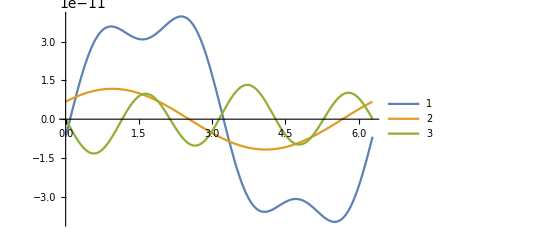

```mathematica
Evec={E1*0+1,E2*0,E3*0};
θrule={θx->0,θz->π/2};
depsr1=Sum[rTensorLNRot[InvVoigtFunc[1][[1]],InvVoigtFunc[1][[2]],i]*Evec[[i]],{i,1,3,1}]/.rVoigtLNvalues/.θrule//Simplify;
depsr2=Sum[rTensorLNRot[InvVoigtFunc[2][[1]],InvVoigtFunc[2][[2]],i]*Evec[[i]],{i,1,3,1}]/.rVoigtLNvalues/.θrule//Simplify;
depsr3=Sum[rTensorLNRot[InvVoigtFunc[3][[1]],InvVoigtFunc[3][[2]],i]*Evec[[i]],{i,1,3,1}]/.rVoigtLNvalues/.θrule//Simplify;
depsr4=Sum[rTensorLNRot[InvVoigtFunc[4][[1]],InvVoigtFunc[4][[2]],i]*Evec[[i]],{i,1,3,1}]/.rVoigtLNvalues/.θrule//Simplify;
depsr5=Sum[rTensorLNRot[InvVoigtFunc[5][[1]],InvVoigtFunc[5][[2]],i]*Evec[[i]],{i,1,3,1}]/.rVoigtLNvalues/.θrule//Simplify;
depsr6=Sum[rTensorLNRot[InvVoigtFunc[6][[1]],InvVoigtFunc[6][[2]],i]*Evec[[i]],{i,1,3,1}]/.rVoigtLNvalues/.θrule//Simplify;

Plot[{depsr1,depsr2,depsr3},{θy,0,2*π},PlotLegends->Automatic]
```

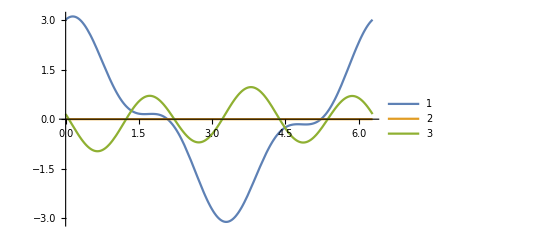

```mathematica
S={S1*0,S2*0+1/2,S3*0,S4*0,S5*0+1/2,S6*0};
θrule={θx->0,θz->π/2};
D1=Sum[eTensorLNRot[1,InvVoigtFunc[J][[1]],InvVoigtFunc[J][[2]]]*S[[J]],{J,1,6,1}]/.eVoigtLNvalues/.θrule//Simplify;
D2=Sum[eTensorLNRot[2,InvVoigtFunc[J][[1]],InvVoigtFunc[J][[2]]]*S[[J]],{J,1,6,1}]/.eVoigtLNvalues/.θrule//Simplify;
D3=Sum[eTensorLNRot[3,InvVoigtFunc[J][[1]],InvVoigtFunc[J][[2]]]*S[[J]],{J,1,6,1}]/.eVoigtLNvalues/.θrule//Simplify;

Plot[{D1,D2,D3},{θy,0,2*π},PlotLegends->Automatic]
```